# Internal Fixed Point

This Mathematica notebook plots individual figures of figure panel 2. It plots the simplex with internal fixed points for varying mate choice bias for the four scenarios:
1) Null case where there is no gene drive
2) Medea drive of 100% efficiency (d = 1)
3) Distortion based gene drive of 100% efficiency (p = 1)
4) When fertility fitness cost c = 0.2

## Defining Functions

These are the general functions of the population dynamics which are later used to plot Simplex (S-3) and their internal fixed points.

```mathematica
xwd[xww_,xdd_] := 1-xww-xdd;
fww [xww_,xdd_,ffww_,ffwd_,ffdd_,p_,d_,e_,h11_,h12_,h22_]:= (h11*ffww*ffww xww xww + h12*(1-p)(1-e/2)*ffww*ffwd xww xwd[xww,xdd] +h12*(1-d)(1-e/2)(1-p)*ffww*ffwd xww xwd[xww,xdd]+ h22*(1-d)(1-p)^2 *ffwd*ffwd xwd[xww,xdd]* xwd[xww,xdd]);
fdd[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ν_,h22_,h23_,h33_] := ν(h33*ffdd*ffdd xdd xdd+ 2 h23*p *ffdd*ffwd xdd xwd[xww,xdd]+ h22* p^2 *ffwd*ffwd xwd[xww,xdd]*xwd[xww,xdd]); 
fwd[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ω_,e_,g_,h12_,h13_,h22_,h23_] := ω(2 h22*p (1-p)*ffwd*ffwd xwd[xww,xdd]*xwd[xww,xdd]+ 2h23*(1-p)*ffdd*ffwd xdd xwd[xww,xdd]+2 h12*(1-e/2)(1-g/2)* p ffww*ffwd xww xwd[xww,xdd]+h13*((2-e)(2-g)/2)*ffdd*ffww xdd xww); 
ftot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,d_,ω_,ν_,e_,g_,h11_,h12_,h13_,h22_,h23_,h33_]:= fww[xww,xdd,ffww,ffwd,ffdd,p,d,e,h11,h12,h22]+fwd[xww,xdd,ffww,ffwd,ffdd,p,ω,e,g,h12,h13,h22,h23]+fdd[xww,xdd,ffww,ffwd,ffdd,p,ν,h22,h23,h33];
xdot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,d_,ω_,ν_,e_,g_,h11_,h12_,h13_,h22_,h23_,h33_] := fww[xww,xdd,ffww,ffwd,ffdd,p,d,e,h11,h12,h22]-xww*ftot[xww,xdd,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33]; 
ydot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,d_,ω_,ν_,e_,g_,h11_,h12_,h13_,h22_,h23_,h33_] := fdd[xww,xdd,ffww,ffwd,ffdd,p,ν,h22,h23,h33]-xdd*ftot[xww,xdd,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33]; 

(* Coordinates of S3 triangle *)
x1 = 0; y1 = 0;
x3 = 0.5; y3 = Sqrt[3]/2;
x2 = 1; y2 = 0;

(* Transforamtion from barycentric to Cartesian *)
xncart[x_,y_] := x1 x+x2 y + x3 (1-x-y);
yncart[x_,y_] := y1 x+y2 y + y3 (1-x-y);
lamda1[xcart_,ycart_]:= ((y2-y3)(xcart-x3)+(x3-x2)(ycart-y3))/((y2-y3)(x1-x3)+(x3-x2)(y1-y3));
lamda2[xcart_,ycart_]:= ((y3-y1)*(xcart-x3)+(x1-x3)(ycart-y3))/((y2-y3)(x1-x3)+(x3-x2)(y1-y3));
xdotcart[xcart_,ycart_,ffww_,ffwd_,ffdd_,p_,d_,ω_,ν_,e_,g_,h11_,h12_,h13_,h22_,h23_,h33_]:=(x1-x3)*xdot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33]+(x2-x3)*ydot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33];
ydotcart[xcart_,ycart_,ffww_,ffwd_,ffdd_,p_,d_,ω_,ν_,e_,g_,h11_,h12_,h13_,h22_,h23_,h33_]:=(y1-y3)*xdot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33]+(y2-y3)*ydot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h12,h13,h22,h23,h33];
𝒟=Triangle[{{x1,y1},{x2,y2},{x3,y3}}];
HWparabola1=Plot[Sqrt[3] x(1-x),{x,0,1},PlotStyle->Black];
```

## Finding fixed point

#### Case-1: Null Case (Varying h)

```mathematica
ffww=1;ffwd=1;ffdd=1;p=0.5;ω=1;ν=1;d=0;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1; 
(*Only h is varied, all other values are fixed to their default value*)

h={0.00001,0.01,0.1,0.99};
nh = Length[h];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]
Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotMarkers->"",PlotStyle->Black,Joined->True]}]
```

{{0.498424,0.00272997},{0.454751,0.0783742},{0.384169,0.200626},{0.293199,0.35819}}

-Graphics-

#### Case-2: Varying h with d=1

{{0.498421,0.00272997},{0.452486,0.0783377},{0.400335,0.154377},{0.365399,0.197975},{0.320292,0.241919},{0.28717,0.262049},{0.258438,0.269189},{0.230769,0.266469},{0.201856,0.254183},{0.169348,0.2305},{0.129981,0.190625},{0.0779447,0.123503},{0.0436519,0.0721487},{0.00971059,0.0166543}}

{{0.498421,0.00272997},{0.452486,0.0783377},{0.400335,0.154377},{0.320292,0.241919},{0.230769,0.266469},{0.129981,0.190625},{0.0779447,0.123503},{0.00971059,0.0166543}}

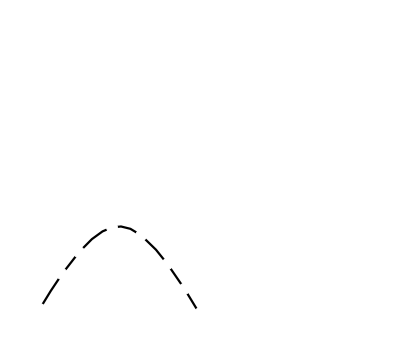

```mathematica
ffww=1;ffwd=1;ffdd=1;p=0.5;ω=1;ν=1;d=1;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
h={0.00001,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.95,0.99};
h2={0.00001,0.01,0.05,0.2,0.5,0.8,0.9,0.99};
nh = Length[h];
nh2 = Length[h2];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]

sol2 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn2,nh2}]]

Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotStyle->Black,Joined->True],ListPlot[sol2,PlotMarkers->"", PlotStyle->Black]}]
```

#### Case-3: Varying h with p=1

{{0.49999,8.66017×10^-6},{0.49,0.00857278},{0.45,0.0410223},{0.4,0.07698},{0.38,0.0897517},{0.35,0.10698},{0.32,0.121666},{0.3,0.129904},{0.25,0.144338},{0.2,0.148461},{0.15,0.139896},{0.1,0.11547},{0.05,0.0708566},{0.01,0.0166413},{0.001,0.00172514}}

{{0.49999,8.66017×10^-6},{0.4,0.07698},{0.3,0.129904},{0.1,0.11547},{0.001,0.00172514}}

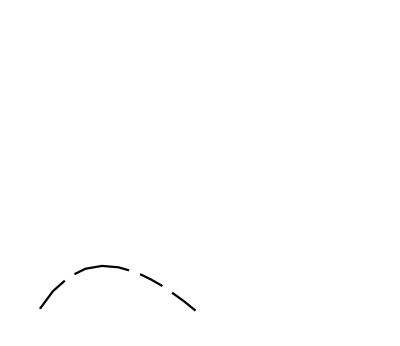

```mathematica
ffww=1;ffwd=1;ffdd=1;p=1.0;ω=1;ν=1;d=0;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
h={0.00001,0.01,0.05,0.1,0.12,0.15,0.18,0.2,0.25,0.3,0.35,0.4,0.45,0.49,0.499};
h2={0.00001,0.1,0.2,0.4,0.499};
nh = Length[h];
nh2 = Length[h2];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.99999,xcart>0.000001,ycart>0.000001},{xcart,ycart}],{hn,nh}]]

sol2 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,xcart<0.99999,xcart>0.000001,ycart>0.000001},{xcart,ycart}],{hn2,nh2}]]

Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotStyle->Black,Joined->True],ListPlot[sol2,PlotMarkers->"", PlotStyle->Black]}]
```

```mathematica
Graphics[{EdgeForm[Thick],GrayLevel[0],Disk[]}]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[Thick],GrayLevel[0.5],Disk[]}]
```

-Graphics-

#### Case-4: Vary h with c=0.2

{{0.60085,0.173477},{0.552764,0.282255},{0.552,0.332554},{0.584094,0.365154},{0.648304,0.366554},{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}],{xcart,ycart}/.First[{}]}

{{0.831673,0.240086},{0.809246,0.263631},{0.777508,0.293317},{0.72307,0.333955},{0.6507,0.365982},{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}],{xcart,ycart}/.Last[{}]}

{0.646611,0.366937}

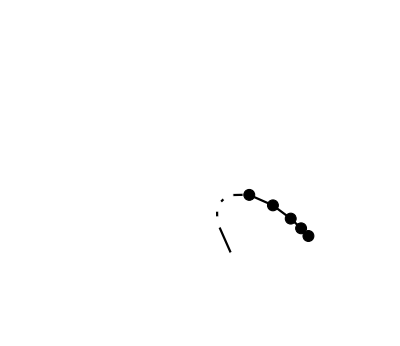

```mathematica
c=0.2;
ffww=1;ffwd=1-c;ffdd=(1-c)^2;p=0.5;ω=1;ν=1;d=0;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
h={0.00001,0.1,0.2,0.3,0.344058,0.4,0.5,0.6,0.7,0.8,0.9,0.95,0.99};
nh = Length[h];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]

sol2 = Quiet[Table[{xcart,ycart}/.Last@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]

sol3 = Quiet[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,0.344,0.344,h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,0.344,0.344,h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}]]

Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotMarkers->"",PlotStyle->Black,Joined->True],ListPlot[sol2,PlotMarkers->"",PlotStyle->Black,Joined->True]}]
```

```mathematica
Graphics[{EdgeForm[Thick],White,Disk[]}]
```

-Graphics-

```mathematica
c=0.2;
ffww=1;ffwd=1-c;ffdd=(1-c)^2;p=0.5;ω=1;ν=1;d=0;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
h={0.34};
nh = Length[h];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]

sol2 = Quiet[Table[{xcart,ycart}/.Last@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]
```

{{0.627865,0.369924}}

{{0.67186,0.359467}}

#### Extra Cases (not in the figure panel): Varying h with d=0.5 and c=0.1

{{0.548596,0.0864516},{0.522681,0.126054},{0.477809,0.193195},{0.448149,0.236448},{0.412865,0.286217},{0.390323,0.316337},{0.373638,0.336982},{0.360088,0.351863},{0.348129,0.362647},{0.336526,0.369991},{0.32373,0.37366},{0.306634,0.371672},{0.294022,0.36647},{0.279527,0.357916}}

{{0.548596,0.0864516},{0.522681,0.126054},{0.477809,0.193195},{0.412865,0.286217},{0.360088,0.351863},{0.32373,0.37366},{0.306634,0.371672},{0.279527,0.357916}}

{{0.912839,0.143736},{0.912409,0.144401},{0.910638,0.147139},{0.903191,0.158556},{0.882758,0.189077},{0.847142,0.239239},{0.827535,0.265079},{0.802459,0.296168}}

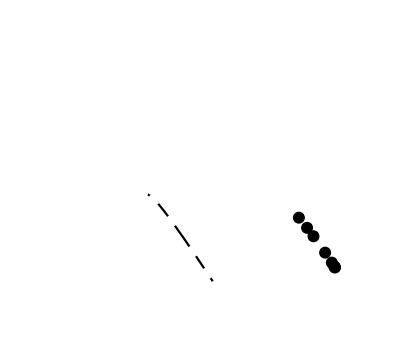

```mathematica
c=0.1;ffww=1;ffwd=1-c;ffdd=(1-c)^2;p=0.5;ω=1;ν=1;d=0.5;e=0;g=0; 
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
h={0.00001,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.95,0.99};
h2={0.00001,0.01,0.05,0.2,0.5,0.8,0.9,0.99};
nh = Length[h];
nh2 = Length[h2];

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h[[hn]],h[[hn]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn,nh}]]

sol2 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn2,nh2}]]

sol3 = Quiet[Table[{xcart,ycart}/.Last@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p,d,ω,ν,e,g,h11,h2[[hn2]],h2[[hn2]],h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{hn2,nh2}]]

Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotStyle->Black,Joined->True],ListPlot[sol2,PlotMarkers->"", PlotStyle->Black],ListPlot[sol3,PlotMarkers->"",PlotStyle->Black]}]
```

#### Extra Cases (not in the figure panel): Varying p

```mathematica
ffww=1;ffwd=1;ffdd=1;p=0.5;d=0;ω=1;ν=1;e=0;g=0;
h = 1; h11=1;h12=h;h13=h;h22=1;h23=1;h33=1;
p={0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.60,0.61,0.62,0.624};
p2={0.5,0.52,0.55,0.57,0.60,0.624};
np = Length[p];
np2 = Length[p2];

sol2 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p2[[pn2]],d,ω,ν,e,g,h11,0.8,0.8,h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p2[[pn2]],d,ω,ν,e,g,h11,0.8,0.8,h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{pn2,np2}]]

sol1 = Quiet[Table[{xcart,ycart}/.First@Solve[ {xdotcart[xcart,ycart,ffww,ffwd,ffdd,p[[pn]],d,ω,ν,e,g,h11,0.8,0.8,h22,h23,h33]==0,ydotcart[xcart,ycart,ffww,ffwd,ffdd,p[[pn]],d,ω,ν,e,g,h11,0.8,0.8,h22,h23,h33]==0,xcart<0.999,xcart>0.0001,ycart>0.0001},{xcart,ycart}],{pn,np}]]
Show[{Graphics[{EdgeForm[Thick],GrayLevel[1],𝒟}],ListPlot[sol1,PlotStyle->Black,Joined->True],ListPlot[sol2,PlotMarkers->"", PlotStyle->Black]}]
```

{{0.3,0.34641},{0.226988,0.288614},{0.145275,0.205261},{0.100644,0.150836},{0.0426074,0.0692248},{0.00162335,0.00280461}}

{{0.3,0.34641},{0.260705,0.317238},{0.226988,0.288614},{0.197118,0.260475},{0.170093,0.232723},{0.145275,0.205261},{0.122229,0.177994},{0.100644,0.150836},{0.0802896,0.123705},{0.0609898,0.0965252},{0.0426074,0.0692248},{0.0250333,0.0417348},{0.00817962,0.0139891},{0.00162335,0.00280461}}

-Graphics-